```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
μtotal = {};
ilist = {"20","22","24","26","28","30","32","34","36","38","40"};
For[i=0,i<11,i++;
iloc = ilist⟦i⟧;
μi = Import["mu" <>  iloc <> ".txt", "Table"];
AppendTo[μtotal,μi]];
```

```mathematica
Show[img,ListPlot[stats3b2, PlotStyle->Blue], ListPlot[stats3b3, PlotStyle->Red],ListPlot[stats3b1, PlotStyle->Green],ListPlot[stats3bmeio, PlotStyle->Purple],PlotRange-> {{0,1},{-1,1}}]
```

```mathematica
μtotal⟦1⟧
```

{{-0.668632,0.0623133},{-0.668632,0.0623133},{-0.668632,0.0623133},{0.139262,-0.000586146},89992,{-0.0716999,0.0219925},{-1.4624,0.0841778},{-1.4624,0.0841778},{-1.4624,0.0841778}}
 |  |  |  |

```mathematica
μtotal⟦1,All,1⟧
```

{-0.668632,-0.668632,-0.668632,0.139262,0.139262,89990,-0.0716999,-0.0716999,-1.4624,-1.4624,-1.4624}
 |  |  |  |

```mathematica
step =   10^-6;
```

```mathematica
maxlist = {};
For[i=0,i< Length[μtotal],i++;
statμi = μtotal⟦i,All,1⟧;
xlist = HistogramList[statμi, {0.15,0.16,step}]⟦1⟧;
peaklist = HistogramList[statμi, {0.15,0.16,step}]⟦2⟧;
AppendTo[maxlist,xlist⟦Flatten[Position[peaklist,Max[peaklist]]]⟦1⟧⟧]]
```

```mathematica
maxlist
```

{0.157338,0.155055,0.155171,0.151981,0.156418,0.153152,0.157953,0.157235,0.156929,0.156535,0.155464}

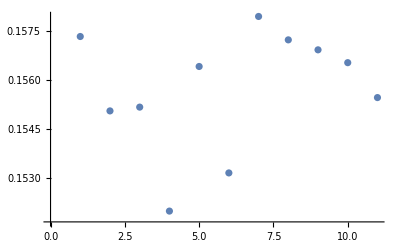

```mathematica
ListPlot[maxlist]
```

```mathematica
HistogramList[μtotal⟦1⟧, {0.15,0.16,step}]
```

{{{0.15,0.150001,0.150002,0.150003,0.150004,0.150005,0.150006,0.150007,0.150008,0.150009,9981,0.159991,0.159992,0.159993,0.159994,0.159995,0.159996,0.159997,0.159998,0.159999,0.16},1},1}
 |  |  |  |

```mathematica
Show[Histogram[μtotal⟦1⟧, {0.15,0.16,step}]]
```

$Aborted

```mathematica
Show[img,ListPlot[stats3b2, PlotStyle->Blue], ListPlot[stats3b3, PlotStyle->Red],ListPlot[stats3b1, PlotStyle->Purple],PlotRange-> {{0.1,0.2},{-0.01,0.01}}]
```

-Graphics-